## Model Setup

```mathematica
wm = ResourceFunction["WolframModel"];
plot = ResourceFunction["WolframModelPlot"];
randomRule = ResourceFunction["RandomWolframModel"];
```

```mathematica
steps=10;
maxValue = 3;
maxVertices=3;
```

```mathematica
randomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
```

```mathematica
signature = randomSignature[3, 3, 2]
```

{{3,1}}→{{3,2}}

```mathematica
signature={{2,2}}->{{4,2}}
```

{{2,2}}→{{4,2}}

```mathematica
init = Array[Function[1],signature[[1]][[1]]]
```

{{1,1},{1,1}}

```mathematica
rule=randomRule[signature]
```

{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}

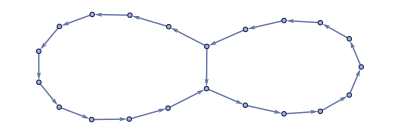

```mathematica
wm[rule, init, steps, "FinalStatePlot"]
```

## Mutations

### Simplest case: retain signature, replace only elements with same range

```mathematica
rule ={rule}
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
selectElement[rule_]:=
Module[{replacement, side, edge, vertex, x},
replacement=RandomInteger[{1, Length[rule]}];
x = rule[[replacement]];
side = RandomInteger[{1, 2}];
x = x[[side]];
edge = RandomInteger[{1, Length[x]}];
x = x[[edge]];
vertex = RandomInteger[{1, Length[x]}];
{replacement, side, edge, vertex}
]
```

```mathematica
maxElement[rule_]:=Max[Flatten[List@@@rule]]
```

```mathematica
rule
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
Extract[rule, {1,1,1,1}]
```

1

```mathematica
rule[[1]][[1]][[1]][[1]]
```

1

```mathematica
replaceRandomElement[rule_]:=
Module[{pos=selectElement[rule]},
ReplacePart[rule, pos->
RandomChoice[Delete[Range[1,maxElement[rule]],Extract[rule, pos]]
]]]
```

```mathematica
rule
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}}

```mathematica
newRule=replaceRandomElement[rule]
```

{{{1,2},{1,3}}→{{1,4},{4,5},{5,1},{3,5}}}

```mathematica
evolution = wm[newRule, init, steps]
```

WolframModelEvolutionObject[…]

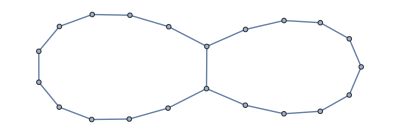

```mathematica
g = Graph@evolution["FinalState"]
```

```mathematica
largestConnectedSubgraph[g_]:=
Subgraph[g, MaximalBy[ConnectedComponents[g], Length]]
```

### Find rules which give connected graphs of increasing dimension

```mathematica
ruleDimension[rule_, nSteps_]:=graphDimension[Graph[wm[rule, {{1,1},{1,1}}, nSteps, "FinalState"]]]
```

```mathematica
graphDimension[graph_] :=
If[ConnectedGraphQ[graph],
 	ResourceFunction["WolframHausdorffDimension"][graph,All, "AllDimensions","VertexMethod" -> Max],
0] // If[NumberQ[#], #, 0]&
```

```mathematica
nextGen[rule_,n_,fitnessFunction_]:=
Module[{baseFitness = fitnessFunction[rule], newRules=<||>, newRule, fitness},
While[Length[newRules]<n,
newRule=replaceRandomElement[rule];
If[!KeyExistsQ[newRules, newRule],
fitness = fitnessFunction[newRule];
If[fitness > baseFitness, newRules[newRule] = fitness];
]
];
newRules
]
```

```mathematica
newRules = nextGen[rule,5,Function[rule, -Abs[ruleDimension[rule] -3]]]
```

<|{{{4,2},{3,2}}→{{4,1},{4,2},{5,4},{3,1}}}→-0.235116,{{{1,2},{4,2}}→{{4,1},{4,2},{5,4},{3,1}}}→-0.525861,{{{1,2},{3,2}}→{{4,3},{4,2},{5,4},{3,1}}}→-0.362916,{{{1,2},{3,5}}→{{4,1},{4,2},{5,4},{3,1}}}→-0.257003,{{{1,5},{3,2}}→{{4,1},{4,2},{5,4},{3,1}}}→-0.387945|>

```mathematica
graphRule[rule_]:=wm[rule,{{1,1},{1,1}},7,"FinalStatePlot"]
```

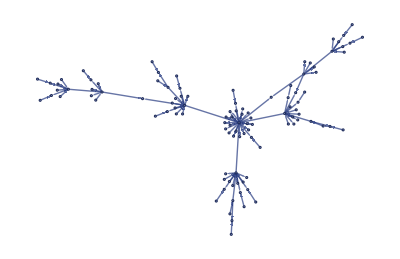
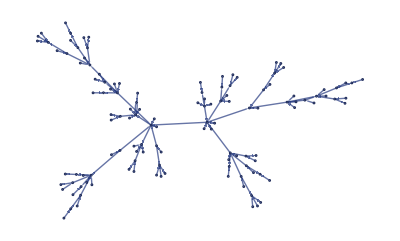
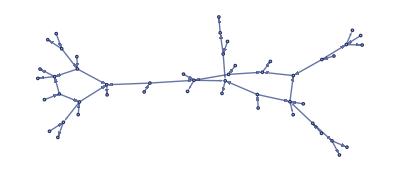
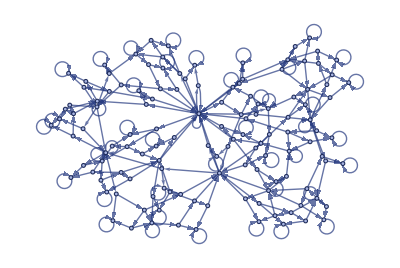
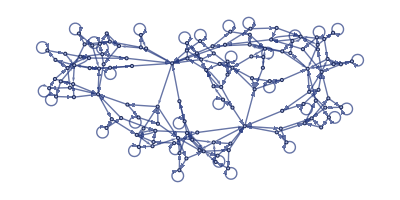

```mathematica
graphRule/@Keys[newRules]
```

```mathematica
evolve[startRule_, fitnessFunction_, nGenerations_, maxTries_:10] :=
Block[
{rule, fitness},
NestList[CompoundExpression[
Do[
rule=replaceRandomElement[First[#]];
fitness=fitnessFunction[rule];
If[fitness >= Last[#], Break],
maxTries
],
{rule, fitness}]&,
{startRule, fitnessFunction[startRule]},
nGenerations]
]
```

```mathematica
evolution = evolve[rule, -Abs[ruleDimension[#, 7] - 3]&, 5]
```

{{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{1,2},{1,3}}→{{1,4},{4,2},{5,2},{3,5}}},-0.892033},{{{{3,2},{1,3}}→{{1,4},{4,2},{5,2},{3,5}}},-0.23278},{{{{3,2},{1,3}}→{{1,4},{1,2},{5,2},{3,5}}},-0.208289},{{{{3,2},{1,3}}→{{1,4},{1,2},{1,2},{3,5}}},-0.192645},{{{{3,2},{1,1}}→{{1,4},{1,2},{1,2},{3,5}}},-0.192645}}

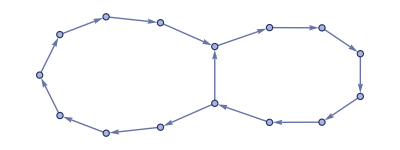
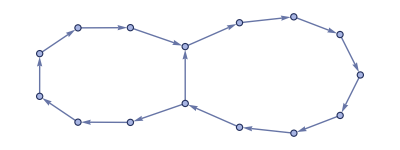
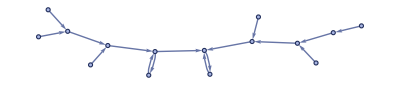
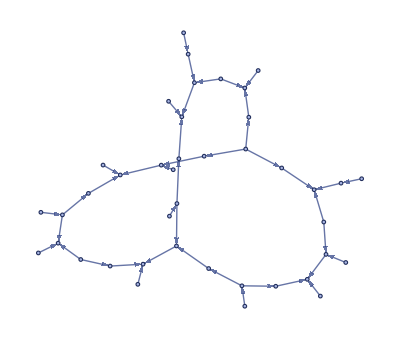
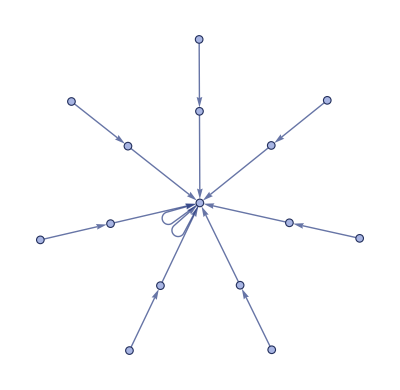
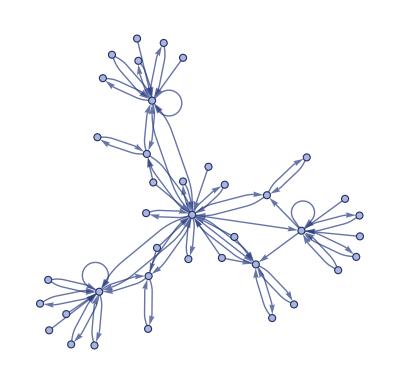
{-Graphics--1.3555,-Graphics--1.3555,-Graphics--1.266,-Graphics--1.23457,-Graphics--0.72483,-Graphics--0.157029}

```mathematica
Labeled[graphRule[First[#]], Last[#]]&/@evolution
```

```mathematica
evolutions = ParallelMap[Function[rule, evolve[rule, -Abs[ruleDimension[#, 7] - 3]&, 5]] , Table[rule, 5]]
```

{{{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{1,2},{1,1}}→{{1,4},{4,5},{5,2},{3,5}}},-1.},{{{{1,2},{2,1}}→{{1,4},{4,5},{5,2},{3,5}}},-1.},{{{{1,2},{2,1}}→{{1,4},{4,5},{5,2},{3,4}}},-1.},{{{{1,4},{2,1}}→{{1,4},{4,5},{5,2},{3,4}}},-0.191628},{{{{1,4},{3,1}}→{{1,4},{4,5},{5,2},{3,4}}},-0.0093376}},{{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{5,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-0.724877},{{{{5,2},{1,1}}→{{1,4},{4,5},{5,2},{3,5}}},-0.678072},{{{{5,2},{1,1}}→{{1,4},{4,1},{5,2},{3,5}}},-0.678072},{{{{5,2},{1,1}}→{{1,4},{4,1},{5,2},{1,5}}},-0.415037},{{{{5,2},{1,1}}→{{1,4},{4,1},{2,2},{1,5}}},-0.0977211}},{{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{1,2},{1,3}}→{{1,3},{4,5},{5,2},{3,5}}},-1.17633},{{{{5,2},{1,3}}→{{1,3},{4,5},{5,2},{3,5}}},-0.838877},{{{{5,2},{1,3}}→{{1,3},{4,5},{5,3},{3,5}}},-0.4646},{{{{5,2},{1,3}}→{{1,3},{4,5},{5,4},{3,5}}},-0.4646},{{{{5,2},{1,3}}→{{1,3},{4,5},{4,4},{3,5}}},-0.324602}},{{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{5,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-0.724877},{{{{5,1},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-0.4591},{{{{5,1},{1,3}}→{{1,5},{4,5},{5,2},{3,5}}},-0.290212},{{{{5,1},{1,3}}→{{1,5},{4,5},{5,2},{3,4}}},-0.237053},{{{{5,1},{1,3}}→{{1,5},{3,5},{5,2},{3,4}}},-0.19562}},{{{{{1,2},{1,3}}→{{1,4},{4,5},{5,2},{3,5}}},-1.3555},{{{{1,2},{4,3}}→{{1,4},{4,5},{5,2},{3,5}}},-0.889871},{{{{1,2},{5,3}}→{{1,4},{4,5},{5,2},{3,5}}},-0.43543},{{{{1,2},{5,3}}→{{1,4},{4,5},{5,3},{3,5}}},-0.43543},{{{{1,2},{5,3}}→{{1,2},{4,5},{5,3},{3,5}}},-0.428975},{{{{1,2},{5,4}}→{{1,2},{4,5},{5,3},{3,5}}},-0.428975}}}

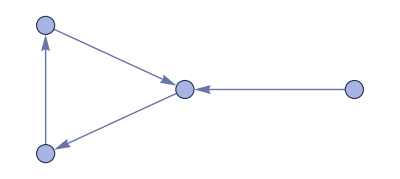
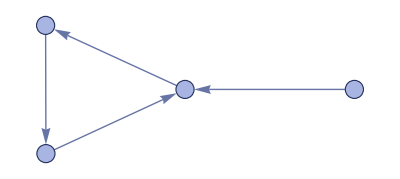
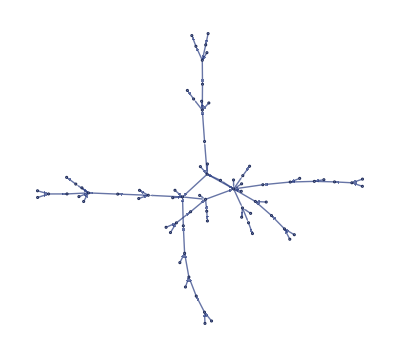
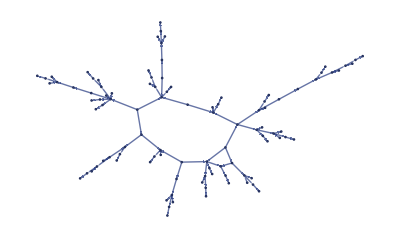
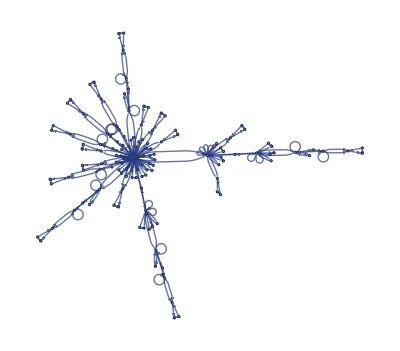
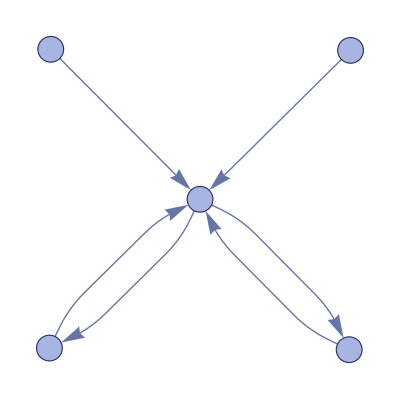
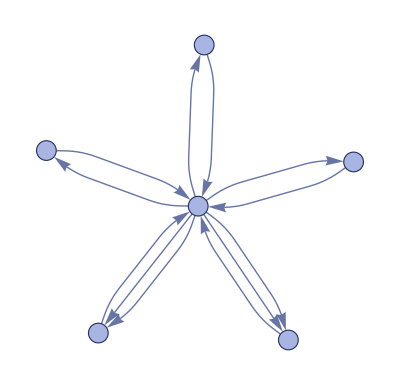
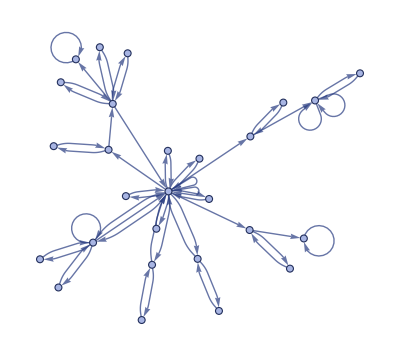
-Graphics--1.3555-Graphics--1.-Graphics--1.-Graphics--1.-Graphics--0.191628-Graphics--0.0093376
-Graphics--1.3555-Graphics--0.724877-Graphics--0.678072-Graphics--0.678072-Graphics--0.415037-Graphics--0.0977211
-Graphics--1.3555-Graphics--1.17633-Graphics--0.838877-Graphics--0.4646-Graphics--0.4646-Graphics--0.324602
-Graphics--1.3555-Graphics--0.724877-Graphics--0.4591-Graphics--0.290212-Graphics--0.237053-Graphics--0.19562
-Graphics--1.3555-Graphics--0.889871-Graphics--0.43543-Graphics--0.43543-Graphics--0.428975-Graphics--0.428975

```mathematica
Column[Function[evolution, Row[Labeled[graphRule[First[#]], Last[#]]&/@evolution]]/@ evolutions]
```

## TODO

#### Issues

Find suspension cause

#### Improvements

Parallelize evolution

#### New fitness functions

Rules whose dimensions stabilize

Different dimension estimates

Edge to vertex ratios

#### Utilities

Track evolution progress

Plot fitness over time

Inset with state plot

Show states across time

Show change in rules across evolution

Plot in rule space

#### Rule Mutations

Add and remove vertices

Add and remove edges

Add and remove replacements

Crossover